```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/Top-EFTphysical_simple-FA/Top-EFTphysical_simple-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## g g → t t (EFT)

in total: 4 Particles insertions

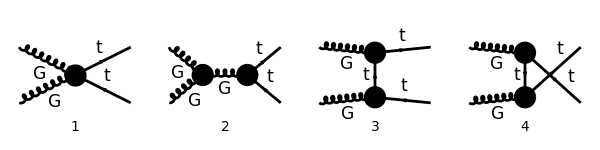

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =    { V[4],V[4]} -> {F[9],-F[9]};
allDiags = InsertFields[tops0,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[3],V[1],S[1],S[2],S[3],V[2],F[1],F[2],F[3],F[4],F[5],F[6],F[7],F[8]},GenericModel->"../../Models/Top-EFTphysical_simple-FA/Top-EFTphysical_simple-FA_FC"];
goodDiags=allDiags;
(* goodDiags=DiagramExtract[allDiags,{1}]; *) 
Paint[goodDiags,ColumnsXRows->{4,1},ImageSize->{ 600,150},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True,SheetHeader->None];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,TransversePolarizationVectors->{k1,k2},FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};

ampB =Simplify[SUNSimplify[DiracSimplify[ampA]]]
(* Remove terms of higher order *)
ampB = Normal[Series[ampB,{yDM,0,2},{gs,0,2}]];
```

in total: 4 Particles amplitudes

(φ(p1,MT)).(γ·ε(k1)).(φ(-p2,MT)) (((k1·ε(k2)+p1·ε(k2)+p2·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(2 ⅈ (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)) gs^2+ⅈ ((2 A0^2 MT (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(2 A0^2 MT (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(2 A0^2 MT (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ·ε(k2)).(γ·k2).(γ̄)^6.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(2 A0^2 MT (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ·ε(k2)).(γ·k2).(γ̄)^7.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(2 A0^2 MT (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(2 A0^2 MT (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ·k2).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(2 A0^2 MT (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ·ε(k2)).(γ·k2).(γ̄)^6.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(2 A0^2 MT (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ·ε(k2)).(γ·k2).(γ̄)^7.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(2 A0^2 (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) k2^2 (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(2 A0^2 (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) k2^2 (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(2 A0^2 (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) k2^2 (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(2 A0^2 (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) k2^2 (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(4 A0^2 (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) (k2·p2) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(4 A0^2 (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) (k2·p2) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(4 A0^2 (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) (k2·p2) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(4 A0^2 (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) (k2·p2) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(4 A0^2 (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ·k2).(γ̄)^6.(φ(-p2,MT)) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(4 A0^2 (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ·k2).(γ̄)^7.(φ(-p2,MT)) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(4 A0^2 (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ·k2).(γ̄)^6.(φ(-p2,MT)) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(4 A0^2 (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ·k2).(γ̄)^7.(φ(-p2,MT)) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(2 A0^2 MT (φ(p2,MT)).(γ·k1).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p1,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(2 A0^2 MT (φ(p2,MT)).(γ·k1).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^7.(φ(-p1,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(2 A0^2 MT (φ(p2,MT)).(γ·k1).(γ·ε(k1)).(γ·ε(k2)).(γ·k2).(γ̄)^6.(φ(-p1,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(2 A0^2 MT (φ(p2,MT)).(γ·k1).(γ·ε(k1)).(γ·ε(k2)).(γ·k2).(γ̄)^7.(φ(-p1,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(2 A0^2 MT (φ(p2,MT)).(γ·ε(k1)).(γ·k1).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p1,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(2 A0^2 MT (φ(p2,MT)).(γ·ε(k1)).(γ·k1).(γ·k2).(γ·ε(k2)).(γ̄)^7.(φ(-p1,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(2 A0^2 MT (φ(p2,MT)).(γ·ε(k1)).(γ·k1).(γ·ε(k2)).(γ·k2).(γ̄)^6.(φ(-p1,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(2 A0^2 MT (φ(p2,MT)).(γ·ε(k1)).(γ·k1).(γ·ε(k2)).(γ·k2).(γ̄)^7.(φ(-p1,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(2 A0^2 (φ(p2,MT)).(γ·k1).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p1,MT)) k2^2 (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(2 A0^2 (φ(p2,MT)).(γ·k1).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^7.(φ(-p1,MT)) k2^2 (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(2 A0^2 (φ(p2,MT)).(γ·ε(k1)).(γ·k1).(γ·ε(k2)).(γ̄)^6.(φ(-p1,MT)) k2^2 (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(2 A0^2 (φ(p2,MT)).(γ·ε(k1)).(γ·k1).(γ·ε(k2)).(γ̄)^7.(φ(-p1,MT)) k2^2 (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(4 A0^2 (φ(p2,MT)).(γ·k1).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p1,MT)) (k2·p1) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(4 A0^2 (φ(p2,MT)).(γ·k1).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^7.(φ(-p1,MT)) (k2·p1) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(4 A0^2 (φ(p2,MT)).(γ·ε(k1)).(γ·k1).(γ·ε(k2)).(γ̄)^6.(φ(-p1,MT)) (k2·p1) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(4 A0^2 (φ(p2,MT)).(γ·ε(k1)).(γ·k1).(γ·ε(k2)).(γ̄)^7.(φ(-p1,MT)) (k2·p1) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(4 A0^2 (φ(p2,MT)).(γ·k1).(γ·ε(k1)).(γ·k2).(γ̄)^6.(φ(-p1,MT)) (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(4 A0^2 (φ(p2,MT)).(γ·k1).(γ·ε(k1)).(γ·k2).(γ̄)^7.(φ(-p1,MT)) (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(4 A0^2 (φ(p2,MT)).(γ·ε(k1)).(γ·k1).(γ·k2).(γ̄)^6.(φ(-p1,MT)) (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(4 A0^2 (φ(p2,MT)).(γ·ε(k1)).(γ·k1).(γ·k2).(γ̄)^7.(φ(-p1,MT)) (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(4 ⅈ A0 gs MT (φ(p1,MT)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) (k2·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(4 ⅈ A0 gs MT (φ(p1,MT)).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) (k2·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(4 ⅈ A0 gs MT (φ(p1,MT)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) (p1·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(4 ⅈ A0 gs MT (φ(p1,MT)).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) (p1·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) (k1·ε(k2)) (p1·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)) (k1·ε(k2)) (p1·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) (k2·ε(k1)) (p1·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)) (k2·ε(k1)) (p1·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(4 ⅈ A0 gs MT (φ(p1,MT)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) (p2·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(4 ⅈ A0 gs MT (φ(p1,MT)).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) (p2·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) (k1·ε(k2)) (p2·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)) (k1·ε(k2)) (p2·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(4 ⅈ A0 gs (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) (p1·ε(k2)) (p2·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(4 ⅈ A0 gs (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)) (p1·ε(k2)) (p2·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) (k2·ε(k1)) (p2·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)) (k2·ε(k1)) (p2·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(4 ⅈ A0 gs (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) (p1·ε(k1)) (p2·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(4 ⅈ A0 gs (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)) (p1·ε(k1)) (p2·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(4 ⅈ A0 gs MT (φ(p1,MT)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)) (k1·ε(k2)+p1·ε(k2)+p2·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(4 ⅈ A0 gs MT (φ(p1,MT)).(γ·ε(k1)).(γ̄)^7.(φ(-p2,MT)) (k1·ε(k2)+p1·ε(k2)+p2·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(4 ⅈ A0 gs MT (φ(p1,MT)).(γ·k1).(γ̄)^6.(φ(-p2,MT)) (ε(k1)·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(4 ⅈ A0 gs MT (φ(p1,MT)).(γ·k1).(γ̄)^7.(φ(-p2,MT)) (ε(k1)·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(4 ⅈ A0 gs MT (φ(p1,MT)).(γ·k2).(γ̄)^6.(φ(-p2,MT)) (ε(k1)·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(4 ⅈ A0 gs MT (φ(p1,MT)).(γ·k2).(γ̄)^7.(φ(-p2,MT)) (ε(k1)·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) (k1·p1) (ε(k1)·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)) (k1·p1) (ε(k1)·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) (k1·p2) (ε(k1)·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)) (k1·p2) (ε(k1)·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) (k2·p1) (ε(k1)·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)) (k2·p1) (ε(k1)·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)) (k2·p2) (ε(k1)·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(2 ⅈ A0 gs (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)) (k2·p2) (ε(k1)·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-gs (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4 A0-gs (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4 A0+gs (φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4 A0+gs (φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(γ̄)^7.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4 A0+(2 A0 gs MT (φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(2 A0 gs MT (φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(2 A0 gs MT (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ·k2).(γ̄)^6.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(2 A0 gs MT (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ·k2).(γ̄)^7.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(A0 gs (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(A0 gs (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(A0 gs (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(A0 gs (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ·k2).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(2 A0 gs (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) k2^2 (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(2 A0 gs (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) k2^2 (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(4 A0 gs (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) (k2·p2) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(4 A0 gs (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) (k2·p2) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(2 A0 gs (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(2 A0 gs (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ̄)^7.(φ(-p2,MT)) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(2 A0 gs (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ̄)^6.(φ(-p2,MT)) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(2 A0 gs (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ̄)^7.(φ(-p2,MT)) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(4 A0 gs (φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ̄)^6.(φ(-p2,MT)) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+(4 A0 gs (φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ̄)^7.(φ(-p2,MT)) (p2·ε(k2)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)+gs (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p2,MT)) (T^Glu2 T^Glu1)_Col3Col4 A0+gs (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^7.(φ(-p2,MT)) (T^Glu2 T^Glu1)_Col3Col4 A0-gs (φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)) (T^Glu2 T^Glu1)_Col3Col4 A0-gs (φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(γ̄)^7.(φ(-p2,MT)) (T^Glu2 T^Glu1)_Col3Col4 A0-(2 A0 gs MT (φ(p2,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^6.(φ(-p1,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(2 A0 gs MT (φ(p2,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(γ̄)^7.(φ(-p1,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(2 A0 gs MT (φ(p2,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ·k2).(γ̄)^6.(φ(-p1,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(2 A0 gs MT (φ(p2,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ·k2).(γ̄)^7.(φ(-p1,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(A0 gs (φ(p1,MT)).(γ·ε(k2)).(γ·k2).(γ·k1).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(A0 gs (φ(p1,MT)).(γ·ε(k2)).(γ·k2).(γ·k1).(γ·ε(k1)).(γ̄)^7.(φ(-p2,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(A0 gs (φ(p1,MT)).(γ·ε(k2)).(γ·k2).(γ·ε(k1)).(γ·k1).(γ̄)^6.(φ(-p2,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(A0 gs (φ(p1,MT)).(γ·ε(k2)).(γ·k2).(γ·ε(k1)).(γ·k1).(γ̄)^7.(φ(-p2,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(2 A0 gs (φ(p2,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p1,MT)) k2^2 (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(2 A0 gs (φ(p2,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^7.(φ(-p1,MT)) k2^2 (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(4 A0 gs (φ(p2,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^6.(φ(-p1,MT)) (k2·p1) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(4 A0 gs (φ(p2,MT)).(γ·ε(k1)).(γ·ε(k2)).(γ̄)^7.(φ(-p1,MT)) (k2·p1) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(2 A0 gs (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT)) (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(2 A0 gs (φ(p1,MT)).(γ·k1).(γ·ε(k1)).(γ̄)^7.(φ(-p2,MT)) (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(2 A0 gs (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ̄)^6.(φ(-p2,MT)) (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(2 A0 gs (φ(p1,MT)).(γ·ε(k1)).(γ·k1).(γ̄)^7.(φ(-p2,MT)) (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(4 A0 gs (φ(p2,MT)).(γ·ε(k1)).(γ·k2).(γ̄)^6.(φ(-p1,MT)) (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)-(4 A0 gs (φ(p2,MT)).(γ·ε(k1)).(γ·k2).(γ̄)^7.(φ(-p1,MT)) (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(ⅈ gs^2 (φ(p1,MT)).(γ·ε(k2)).(φ(-p2,MT)) (k2·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(ⅈ gs^2 (φ(p1,MT)).(γ·ε(k2)).(φ(-p2,MT)) (p1·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(ⅈ gs^2 (φ(p1,MT)).(γ·ε(k2)).(φ(-p2,MT)) (p2·ε(k1)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(ⅈ gs^2 (φ(p1,MT)).(γ·k1).(φ(-p2,MT)) (ε(k1)·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2-(ⅈ gs^2 (φ(p1,MT)).(γ·k2).(φ(-p2,MT)) (ε(k1)·ε(k2)) f^Glu1Glu2Glu5 T_Col3Col4^Glu5)/(p1+p2)^2+(gs^2 (φ(p1,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(φ(-p2,MT)) (T^Glu1 T^Glu2)_Col3Col4)/((k2-p2)^2-MT^2)-(gs^2 (φ(p2,MT)).(γ·ε(k1)).(γ·k2).(γ·ε(k2)).(φ(-p1,MT)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2)+(2 gs^2 (φ(p2,MT)).(γ·ε(k1)).(φ(-p1,MT)) (p1·ε(k2)) (T^Glu2 T^Glu1)_Col3Col4)/((k2-p1)^2-MT^2))

```mathematica
ampC=DiracSimplify[ampB]
```

ⅈ A0 gs (T^Glu1 T^Glu2)_Col3Col4 (φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT))+ⅈ A0 gs (T^Glu1 T^Glu2)_Col3Col4 (φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(γ̄)^7.(φ(-p2,MT))-ⅈ A0 gs (T^Glu2 T^Glu1)_Col3Col4 (φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(γ̄)^6.(φ(-p2,MT))-ⅈ A0 gs (T^Glu2 T^Glu1)_Col3Col4 (φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(γ̄)^7.(φ(-p2,MT))-ⅈ A0 gs (T^Glu1 T^Glu2)_Col3Col4 (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(φ(-p2,MT))+ⅈ A0 gs (T^Glu2 T^Glu1)_Col3Col4 (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(φ(-p2,MT))

```mathematica
(* Remove SM contribution *)
ampSM=gs^2 SeriesCoefficient[ampC,{gs,0,2},{yDM,0,0}];
ampC=Simplify[ampC-ampSM];
```

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,MT,MT,0,0];
```

```mathematica
ampEsimp=FullSimplify[DotSimplify[DiracSimplify[ampC/.{DiracGamma[7]->1-DiracGamma[6]}]]]
```

-ⅈ A0 gs ((T^Glu1 T^Glu2)_Col3Col4-(T^Glu2 T^Glu1)_Col3Col4) ((φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(φ(-p2,MT))-(φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(φ(-p2,MT)))

```mathematica
DiracSimplify[%]
```

-ⅈ A0 gs (T^Glu1 T^Glu2)_Col3Col4 (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(φ(-p2,MT))+ⅈ A0 gs (T^Glu1 T^Glu2)_Col3Col4 (φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(φ(-p2,MT))+ⅈ A0 gs (T^Glu2 T^Glu1)_Col3Col4 (φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(φ(-p2,MT))-ⅈ A0 gs (T^Glu2 T^Glu1)_Col3Col4 (φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(φ(-p2,MT))

```mathematica
sub={DiracGamma[Momentum[Polarization[k1,I,Transversality->True],D],D].DiracGamma[Momentum[Polarization[k2,I,Transversality->True]]]-> -DiracGamma[Momentum[Polarization[k2,I,Transversality->True],D],D].DiracGamma[Momentum[Polarization[k1,I,Transversality->True]]]+2Pair[Polarization[k1,I,Transversality->True],Polarization[k2,I,Transversality->True]]};
```

```mathematica
spinorChains=Tally[Cases[{ampEsimp},Spinor[___].___.Spinor[___],All]][[All,1]]
pairs=Cases2[ampEsimp,Pair]
```

{(φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(φ(-p2,MT)),(φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(φ(-p2,MT))}

{}

### Coefficients for each term

```mathematica
Table[{spinorChains[[i]],FullSimplify[Coefficient[ampEsimp,spinorChains[[i]]]]},{i,1,Length[spinorChains]}]
```

((φ(p1,MT)).(γ·ε(k1)).(γ·ε(k2)).(φ(-p2,MT)) | -ⅈ A0 gs ((T^Glu1 T^Glu2)_Col3Col4-(T^Glu2 T^Glu1)_Col3Col4)
(φ(p1,MT)).(γ·ε(k2)).(γ·ε(k1)).(φ(-p2,MT)) | ⅈ A0 gs ((T^Glu1 T^Glu2)_Col3Col4-(T^Glu2 T^Glu1)_Col3Col4))

```mathematica
A0eft=-gs yDM^2 MT/(384 Pi^2)1/((mST^2-mChi^2)^4)(3 mChi^4 mST^2-6 mChi^2 mST^4 + 6 mST^4 mChi^2 Log[mST^2/mChi^2]+2 mChi^6 mST^6);
```